```mathematica
<<Local`QFTToolKit`
Put[SaveFile=NBname["stub"]<>".out"];
```

5.2 Bhabha scattering. Compute the differential cross section

● Compute the differential cross section for Bhabha scattering: e^- e^+→e^- e^+
There are 2 first order diagrams: {e^-,e^+}→{e^-,e^+}

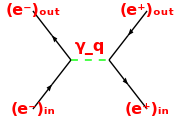
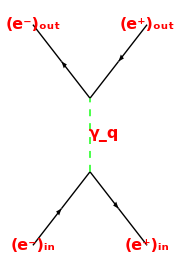

```mathematica
PR[CO["● Compute the differential cross section for Bhabha scattering: ",SuperPlus[e] SuperMinus[e]->SuperPlus[e] SuperMinus[e]],
NL,"There are 2 first order diagrams: ",{SuperMinus[e],SuperPlus[e]}->{SuperMinus[e],SuperPlus[e]}
]
PR[{vx,line}=GraphicPointLines[7,5,{{{0,0},{2,2}},{{2,2},{0,4}},{{2,2},{4,2}},{{4,2},{6,4}},{{4,2},{6,0}}},False];
Linex[i_]:=Line[line[[i]]];
font:={Red,Bold,16};
Graphics[{(*Thick,*)Black,
MidArrow[line[[1]]],
MidArrow[line[[2]]],
MidArrow[line[[5]]],
MidArrow[line[[4]]//Reverse],
{Dashed,Green,Thick,Linex[3]},
Text[Style[Subscript[(SuperMinus[e]), in],font],vx[[1]]],
Text[Style[Subscript[(SuperMinus[e]), out],font],vx[[5]]],
Text[Style[Subscript[(SuperPlus[e]), in],font],vx[[31]]],
Text[Style[Subscript[(SuperPlus[e]), out],font],vx[[35]]],
MidLineTextOffset[Subscript[γ, q],vx[[18]],font,{0.5,.02}]
},ImageSize->Small],
{vx,line}=GraphicPointLines[5,7,{{{0,0},{2,2}},{{2,2},{4,0}},{{2,2},{2,4}},{{2,4},{4,6}},{{2,4},{0,6}}},False];
Graphics[{(*Thick,*)Black,
MidArrow[line[[1]]],
MidArrow[line[[2]]],
MidArrow[line[[5]]],
MidArrow[line[[4]]//Reverse],
{Dashed,Green,Thick,Linex[3]},
Text[Style[Subscript[(SuperMinus[e]), in],font],vx[[1]]],
Text[Style[Subscript[(SuperMinus[e]), out],font],vx[[7]]],
Text[Style[Subscript[(SuperPlus[e]), in],font],vx[[29]]],
Text[Style[Subscript[(SuperPlus[e]), out],font],vx[[35]]],
MidLineTextOffset[Subscript[γ, q],vx[[18]],font,{0.,.5}]
},ImageSize->Small]
]
```

```mathematica
v[q_,i_]:=Subscript[q⃗, i]
tu[q_,μ_]:=T[q,"u"][μ]
td[q_,μ_]:=T[q,"d"][μ]
"Lorentz invariance"
$sLv=tu[Subscript[q_, a_],μ_]td[Subscript[q_, b_],μ_]->tu[Subscript[q, a],0]td[Subscript[q, b],0]-v[q,a].v[q,b]
"Massless condition"
$m0={Subscript[m, _]->0,Abs[v[p,e[in]]]->tu[Subscript[p, e[in]],0]}
```

Lorentz invariance

q__a__μ_^μ_ q__b__μ_^μ_→-(q⃗)_a.(q⃗)_b+q_a_0^0 q_b_0^0

Massless condition

{m__→0,Abs[(p⃗)_e[in]]→p_e[in]_0^0}

```mathematica
PR["• Amplitudes for each diagram: ",
$M1=Subscript[ℳ, t]->-I e^2/(tu[Subscript[q, 1],μ1].td[Subscript[q, 1],μ1])
(ū[Subscript[p, e[out]]].T[γ,"u"][ν1].u[Subscript[p, e[in]]]
v̄[Subscript[p, ē[in]]].T[γ,"d"][ν1].v[Subscript[p, ē[out]]] ),
and,
$M2=Subscript[ℳ, s]->I e^2/(tu[Subscript[q, 2],μ2].td[Subscript[q, 2],μ2])
(ū[Subscript[p, e[out]]].T[γ,"u"][ν2].v[Subscript[p, ē[out]]]
v̄[Subscript[p, ē[in]]].T[γ,"d"][ν2].u[Subscript[p, e[in]]] ),
NL,"where ",
$qt={T[Subscript[q, 1],"u"][μ_]->-T[Subscript[p, e[in]],"u"][μ]+T[Subscript[p, e[out]],"u"][μ],T[Subscript[q, 2],"u"][μ_]->T[Subscript[p, e[in]],"u"][μ]+T[Subscript[p, ē[in]],"u"][μ],
T[Subscript[q, 3],"u"][μ_]->-T[Subscript[p, e[in]],"u"][μ]+T[Subscript[p, ē[out]],"u"][μ]},
NL,"Total amplitude: ",
$M=ℳ->AddRules[{$M1,$M2}][[2]],
NL,"The Square magnitude summed over spins: ","POFF",
$=OpRules[{Thread[Conjugate[$M/.{ν1->ν1c,ν2->ν2c}],Rule],$M},Times],
$real={e,Subscript[q⃗, _],tu[Subscript[q, _],_],td[Subscript[q, _],_],1/Subscript[q⃗, _].Subscript[q⃗, _]};$scalar={e,Subscript[p, _],Tensor[Subscript[p, _],_,_],v[q,1].v[q,1],1/Subscript[q⃗, _].Subscript[q⃗, _],Subscript[q⃗, _].Subscript[q⃗, _],ℳ,Subscript[m, _],Tensor[g,_,_]},
Yield,$=$//ConjugateSimplify[$real],"POFF",
NL,"Apply: ",$s=Conjugate[OverBar[u_][pu_]].Conjugate[tt:Tensor[γ,a_,b_]].Conjugate[v_[pv_]]->v̄ [pv]. tt.u[pu],
Yield,$=$/.$s//Expand,"PONdd",
Yield,xtmp=$=$/.groupUUpp[Subscript[p, e[out]]]/.groupUUpp[Subscript[p, ē[out]]]/.groupUUpp[Subscript[p, e[in]]]/.groupUUpp[Subscript[p, ē[in]]],
NL,"Sum over spin (Implied Tr over Dot[] expression.): ","POFF",
$=$//.scatteringAmplitudeRules//simpleDot3[$scalar],"PON",
$pass8=$=$/.dd:Dot[_,__]:>Tr[dd]/;FreeQ[dd,q]//simpleTrGamma1[$scalar]//MetricContractAll[g,4]
]
```

• Amplitudes for each diagram: ℳ_t→-(ⅈ e^2 ū[p_e[out]].γ_ν1^ν1.u[p_e[in]] v̄[p_(ē[in])].γ_ν1^ν1.v[p_(ē[out])])/(q_1_μ1^μ1.q_1_μ1^μ1) and ℳ_s→(ⅈ e^2 ū[p_e[out]].γ_ν2^ν2.v[p_(ē[out])] v̄[p_(ē[in])].γ_ν2^ν2.u[p_e[in]])/(q_2_μ2^μ2.q_2_μ2^μ2)
where {q_1_μ_^μ_→-p_e[in]_μ^μ+p_e[out]_μ^μ,q_2_μ_^μ_→p_e[in]_μ^μ+(p_(ē[in]))_μ^μ,q_3_μ_^μ_→-p_e[in]_μ^μ+(p_(ē[out]))_μ^μ}
Total amplitude: ℳ→-(ⅈ e^2 ū[p_e[out]].γ_ν1^ν1.u[p_e[in]] v̄[p_(ē[in])].γ_ν1^ν1.v[p_(ē[out])])/(q_1_μ1^μ1.q_1_μ1^μ1)+(ⅈ e^2 ū[p_e[out]].γ_ν2^ν2.v[p_(ē[out])] v̄[p_(ē[in])].γ_ν2^ν2.u[p_e[in]])/(q_2_μ2^μ2.q_2_μ2^μ2)
The Square magnitude summed over spins: 
.......
→ ℳ ℳ^*→1/((q_1_μ1^μ1.q_1_μ1^μ1)^2)e^4 ū[p_e[in]].γ_ν1c^ν1c.u[p_e[out]].ū[p_e[out]].γ_ν1^ν1.u[p_e[in]] v̄[p_(ē[in])].γ_ν1^ν1.v[p_(ē[out])].v̄[p_(ē[out])].γ_ν1c^ν1c.v[p_(ē[in])]+1/((q_2_μ2^μ2.q_2_μ2^μ2)^2)e^4 v̄[p_(ē[in])].γ_ν2^ν2.u[p_e[in]].ū[p_e[in]].γ_ν2c^ν2c.v[p_(ē[in])] v̄[p_(ē[out])].γ_ν2c^ν2c.u[p_e[out]].ū[p_e[out]].γ_ν2^ν2.v[p_(ē[out])]-1/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)e^4 v̄[p_(ē[in])].γ_ν1^ν1.v[p_(ē[out])].v̄[p_(ē[out])].γ_ν2c^ν2c.u[p_e[out]].ū[p_e[out]].γ_ν1^ν1.u[p_e[in]].ū[p_e[in]].γ_ν2c^ν2c.v[p_(ē[in])]-1/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)e^4 v̄[p_(ē[in])].γ_ν2^ν2.u[p_e[in]].ū[p_e[in]].γ_ν1c^ν1c.u[p_e[out]].ū[p_e[out]].γ_ν2^ν2.v[p_(ē[out])].v̄[p_(ē[out])].γ_ν1c^ν1c.v[p_(ē[in])]
Sum over spin (Implied Tr over Dot[] expression.): ℳ ℳ^*→(64 e^4 m_e[in] m_e[out] m_(ē[in]) m_(ē[out]))/((q_1_μ1^μ1.q_1_μ1^μ1)^2)+(64 e^4 m_e[in] m_e[out] m_(ē[in]) m_(ē[out]))/((q_2_μ2^μ2.q_2_μ2^μ2)^2)+(64 e^4 m_e[in] m_e[out] m_(ē[in]) m_(ē[out]))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)-(16 e^4 m_(ē[in]) m_(ē[out]) p_e[in]_($18)^($18) p_e[out]_($18)^($18))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)-(32 e^4 m_(ē[in]) m_(ē[out]) p_e[in]_($5)^($5) p_e[out]_($5)^($5))/((q_1_μ1^μ1.q_1_μ1^μ1)^2)-(16 e^4 m_(ē[in]) m_(ē[out]) p_e[in]_($15)^($15) p_e[out]_($15)^($15))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(16 e^4 m_e[in] m_(ē[out]) p_e[out]_($14)^($14) (p_(ē[in]))_($14)^($14))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(16 e^4 m_e[out] m_(ē[out]) p_e[in]_($15)^($15) (p_(ē[in]))_($15)^($15))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(16 e^4 m_e[out] m_(ē[out]) p_e[in]_($17)^($17) (p_(ē[in]))_($17)^($17))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(16 e^4 m_e[in] m_(ē[out]) p_e[out]_($18)^($18) (p_(ē[in]))_($18)^($18))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(32 e^4 m_e[out] m_(ē[out]) p_e[in]_($9)^($9) (p_(ē[in]))_($9)^($9))/((q_2_μ2^μ2.q_2_μ2^μ2)^2)-(16 e^4 m_e[in] m_e[out] (p_(ē[in]))_($13)^($13) (p_(ē[out]))_($13)^($13))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(16 e^4 m_e[out] m_(ē[in]) p_e[in]_($19)^($19) (p_(ē[out]))_($19)^($19))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(16 e^4 m_e[in] m_(ē[in]) p_e[out]_($19)^($19) (p_(ē[out]))_($19)^($19))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(32 e^4 p_e[in]_($19)^($19) p_e[out]_($18)^($18) (p_(ē[in]))_($18)^($18) (p_(ē[out]))_($19)^($19))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)-(16 e^4 m_e[in] m_e[out] (p_(ē[in]))_($19)^($19) (p_(ē[out]))_($19)^($19))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(32 e^4 p_e[in]_($7)^($7) p_e[out]_($6)^($6) (p_(ē[in]))_($6)^($6) (p_(ē[out]))_($7)^($7))/((q_1_μ1^μ1.q_1_μ1^μ1)^2)+(32 e^4 p_e[in]_($6)^($6) p_e[out]_($7)^($7) (p_(ē[in]))_($6)^($6) (p_(ē[out]))_($7)^($7))/((q_1_μ1^μ1.q_1_μ1^μ1)^2)-(32 e^4 m_e[in] m_e[out] (p_(ē[in]))_($7)^($7) (p_(ē[out]))_($7)^($7))/((q_1_μ1^μ1.q_1_μ1^μ1)^2)+(32 e^4 m_e[in] m_(ē[in]) p_e[out]_($11)^($11) (p_(ē[out]))_($11)^($11))/((q_2_μ2^μ2.q_2_μ2^μ2)^2)+(16 e^4 m_e[in] m_(ē[in]) p_e[out]_($14)^($14) (p_(ē[out]))_($14)^($14))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(16 e^4 m_e[out] m_(ē[in]) p_e[in]_($15)^($15) (p_(ē[out]))_($15)^($15))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(32 e^4 p_e[in]_($15)^($15) p_e[out]_($14)^($14) (p_(ē[in]))_($14)^($14) (p_(ē[out]))_($15)^($15))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(32 e^4 p_e[in]_($9)^($9) p_e[out]_($9)^($9) (p_(ē[in]))_($8)^($8) (p_(ē[out]))_($8)^($8))/((q_2_μ2^μ2.q_2_μ2^μ2)^2)+(32 e^4 p_e[in]_($9)^($9) p_e[out]_($8)^($8) (p_(ē[in]))_($8)^($8) (p_(ē[out]))_($9)^($9))/((q_2_μ2^μ2.q_2_μ2^μ2)^2)

```mathematica
PR[CG["• Apply Lorentz invariances and CM condition: "],
NL,
$scm={Subscript[p⃗, ē[in]]->-Subscript[p⃗, e[in]],Subscript[p⃗, ē[out]]->-Subscript[p⃗, e[out]],
Subscript[p⃗, e[in]].Subscript[p⃗, e[out]]|Subscript[p⃗, e[out]].Subscript[p⃗, e[in]]->Abs[Subscript[p⃗, e[in]]]Abs[Subscript[p⃗, e[out]]]Cos[θ],Subscript[p⃗, e[in_]].Subscript[p⃗, e[in_]]->T[Subscript[p, e[in]],"u"][0]T[Subscript[p, e[in]],"u"][0]-Subscript[m, e[in]]^2,
T[Subscript[p, i1_],"u"][i_]T[Subscript[p, i2_],"d"][i_]->T[Subscript[p, i2],"u"][0]T[Subscript[p, i1],"u"][0]-Subscript[p⃗, i1]. Subscript[p⃗, i2],
Subscript[m, e[out]]->Subscript[m, e[in]],Subscript[m, ē[out]]->Subscript[m, ē[in]]
},"POFF",
Yield,$=$pass8//.$scm//simpleDot3[{}];
Yield,$=$//.$scm,
"PONdd",
NL,"And equal mass condition (only apply to implied Abs[p⃗] expressions.): ",
$sem={Subscript[m, ē[in]]->Subscript[m, e[in]],
Subscript[m, e[in_]]->Subscript[m, e],
T[Subscript[p, ē[_]],"u"][0]|T[Subscript[p, e[_]],"u"][0]->T[Subscript[p, e[in]],"u"][0],
Abs[Subscript[p⃗, e[out]]]->Abs[Subscript[p⃗, e[in]]],
T[Subscript[p, i_],"u"][0]^2->Subscript[m, i]^2+Abs[Subscript[p⃗, i]]^2,
T[Subscript[p, i_],"u"][0]^4->(Subscript[m, i]^2+Abs[Subscript[p⃗, i]]^2)^2,
T[Subscript[p, i_],"u"][0]^-2->(Subscript[m, i]^2+Abs[Subscript[p⃗, i]]^2)^-1},"POFF",
Yield,$MM=$=$//.$sem//Simplify;ColumnSumExp[$]//Framed
]
PR["• The differential cross-section using (4.84): ",$=e484=xD[d][σ,Ω]->1/(2 T[Subscript[p, ē[in]],"u"][0]2T[Subscript[p, e[in]],"u"][0]Abs[(Subscript[p⃗, e[in]]/T[Subscript[p, e[in]],"u"][0]-Subscript[p⃗, ē[in]]/T[Subscript[p, ē[in]],"u"][0])])(Abs[Subscript[p⃗, e[in]]]/((2π)^2  4(T[Subscript[p, ē[in]],"u"][0]+T[Subscript[p, e[in]],"u"][0])))ℳ Conjugate[ℳ],
NL,"In CM and equal mass: ",
Yield,$=$/.$scm//.$sem,CK,
Yield,$pass9=$=$/.$MM
]
```

• Apply Lorentz invariances and CM condition: 
{(p⃗)_(ē[in])→-(p⃗)_e[in],(p⃗)_(ē[out])→-(p⃗)_e[out],(p⃗)_e[in].(p⃗)_e[out]|(p⃗)_e[out].(p⃗)_e[in]→Abs[(p⃗)_e[in]] Abs[(p⃗)_e[out]] Cos[θ],(p⃗)_e[in_].(p⃗)_e[in_]→-m_e[in]^2+(p_e[in]_0^0)^2,p_i1__i_^i_ p_i2__i_^i_→-(p⃗)_i1.(p⃗)_i2+p_i1_0^0 p_i2_0^0,m_e[out]→m_e[in],m_(ē[out])→m_(ē[in])}
.......
And equal mass condition (only apply to implied Abs[p⃗] expressions.): {m_(ē[in])→m_e[in],m_e[in_]→m_e,(p_(ē[_]))_0^0|p_e[_]_0^0→p_e[in]_0^0,Abs[(p⃗)_e[out]]→Abs[(p⃗)_e[in]],(p_i__0^0)^2→Abs[(p⃗)_i]^2+m_i^2,(p_i__0^0)^4→(Abs[(p⃗)_i]^2+m_i^2)^2,(p_i__0^0)^-2→1/(Abs[(p⃗)_i]^2+m_i^2)}

• The differential cross-section using (4.84): (d̲)_Ω[σ]→(ℳ Abs[(p⃗)_e[in]] ℳ^*)/(64 π^2 Abs[((p⃗)_e[in])/(p_e[in]_0^0)-((p⃗)_(ē[in]))/((p_(ē[in]))_0^0)] p_e[in]_0^0 (p_(ē[in]))_0^0 (p_e[in]_0^0+(p_(ē[in]))_0^0))
In CM and equal mass: 
→ (d̲)_Ω[σ]→(ℳ Abs[(p⃗)_e[in]] ℳ^*)/(256 π^2 Abs[((p⃗)_e[in])/(p_e[in]_0^0)] (p_e[in]_0^0)^3)⟵CHECK
→ (d̲)_Ω[σ]→(e^4 Abs[(p⃗)_e[in]] (Abs[(p⃗)_e[in]]^4 (2 (3+Cos[2 θ]) (q_1_μ1^μ1.q_1_μ1^μ1)^2+16 Cos[θ/2]^4 q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2+(11+4 Cos[θ]+Cos[2 θ]) (q_2_μ2^μ2.q_2_μ2^μ2)^2)+8 Abs[(p⃗)_e[in]]^2 (2 (q_1_μ1^μ1.q_1_μ1^μ1)^2+4 Cos[θ/2]^2 q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2+(1+Cos[θ]) (q_2_μ2^μ2.q_2_μ2^μ2)^2) m_e^2+4 (3 (q_1_μ1^μ1.q_1_μ1^μ1)^2+3 q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2+(q_2_μ2^μ2.q_2_μ2^μ2)^2) m_e^4))/(16 π^2 Abs[((p⃗)_e[in])/(p_e[in]_0^0)] (q_1_μ1^μ1.q_1_μ1^μ1)^2 (q_2_μ2^μ2.q_2_μ2^μ2)^2 (p_e[in]_0^0)^3)

```mathematica
PR[CG["• For massless case: "],$s={Subscript[m, e]->0,tu[Subscript[p, e[in]],0]->Abs[Subscript[p⃗, e[in]]]},
Yield,$=$pass9/.$s/.$sem//FullSimplify;$=$/.$m0;ColumnSumExp[$]
]
```

• For massless case: {m_e→0,p_e[in]_0^0→Abs[(p⃗)_e[in]]}
→ (d̲)_Ω[σ]→(e^4 ∑[(11+4 Cos[θ]+Cos[2 θ])/((q_1_μ1^μ1.q_1_μ1^μ1)^2)
(2 (3+Cos[2 θ]))/((q_2_μ2^μ2.q_2_μ2^μ2)^2)
(16 Cos[θ/2]^4)/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)] (p_e[in]_0^0)^2)/(16 π^2)

```mathematica
PR[CG["• Definition of Mandelstam variables: "],
$mendalstam= Thread[{t,s,u}->{T[Subscript[q, 1],"u"][μ]T[Subscript[q, 1],"d"][μ],T[Subscript[q, 2],"u"][μ]T[Subscript[q, 2],"d"][μ],T[Subscript[q, 3],"u"][μ]T[Subscript[q, 3],"d"][μ]}];Column[$mendalstam],
NL,"where: ",
$qt={T[Subscript[q, 1],"u"][μ_]->-T[Subscript[p, e[in]],"u"][μ]+T[Subscript[p, e[out]],"u"][μ],T[Subscript[q, 2],"u"][μ_]->T[Subscript[p, e[in]],"u"][μ]+T[Subscript[p, ē[in]],"u"][μ],
T[Subscript[q, 3],"u"][μ_]->-T[Subscript[p, e[in]],"u"][μ]+T[Subscript[p, ē[out]],"u"][μ]
};
$qt=Flatten[Append[$qt,LowerIndexTU1[{μ,μ_},{μ,μ_}][$qt]]];Column[$qt],"POFF",
Yield,$mend1=$mendalstam/.$qt;Column[$mend1],
Yield,$mend1=$mend1//Expand//OrderTensorDummyIndices;
"PONdd",
NL,Column[$mend1],
NL,CG["• Equal mass CM collisions Compute different quantites of [t,s,u]."],
NL,"Lorentz invariant Rule: ",$sLv,
and,$scm1=Subscript[p⃗, ē[in]]->-Subscript[p⃗, e[in]],Subscript[p⃗, ē[out]]->-Subscript[p⃗, e[out]],Subscript[p⃗, e[in_]].Subscript[p⃗, e[in_]]->T[Subscript[p, e[in]],"u"][0]T[Subscript[p, e[in]],"u"][0]-Subscript[m, e[in]]^2,
NL,
$s={T[Subscript[p, i_],"u"][μ_]T[Subscript[p, i_],"d"][μ_]->Subscript[m, i]^2,xT[Subscript[p, i_],"u"][μ_]T[Subscript[p, j_],"d"][μ_]->T[Subscript[p, i],"u"][0]T[Subscript[p, j],"u"][0]-Subscript[p⃗, i].Subscript[p⃗, j],Subscript[m, _]->Subscript[m, e]},
Yield,$=$mend1//.$s;ColumnSumExp[$];
Yield,$m1=RuleX[$,Tensor[Subscript[p, a_],_,_]Tensor[Subscript[p, b_],_,_]]//RulesVarPattern[{μ}];Column[$m1]//Framed,

NL,"Alternatively, ",
$qt2={T[Subscript[q, 1],"u"][μ_]->-T[Subscript[p, ē[in]],"u"][μ]+T[Subscript[p, ē[out]],"u"][μ],T[Subscript[q, 2],"u"][μ_]->T[Subscript[p, e[out]],"u"][μ]+T[Subscript[p, ē[out]],"u"][μ],
T[Subscript[q, 3],"u"][μ_]->-T[Subscript[p, e[out]],"u"][μ]+T[Subscript[p, ē[in]],"u"][μ]};Column[$qt2],"POFF",
$qt2=Flatten[Append[$qt2,LowerIndexTU1[{μ,μ_},{μ,μ_}][$qt2]]],
Yield,$mend2=$mendalstam/.$qt2;Column[$mend2],
Yield,$mend2=$mend2//Expand//OrderTensorDummyIndices;
"PONdd",
NL,Column[$mend2],
NL,"• Compute different quantites [t,s,u] for equal mass collision in CM frame.",
NL,"Lorentz invariant Rule: ",$sLv,
and,$scm1=Subscript[p⃗, ē[in]]->-Subscript[p⃗, e[in]],Subscript[p⃗, ē[out]]->-Subscript[p⃗, e[out]],Subscript[p⃗, e[in_]].Subscript[p⃗, e[in_]]->T[Subscript[p, e[in]],"u"][0]T[Subscript[p, e[in]],"u"][0]-Subscript[m, e[in]]^2,
NL,
$s={T[Subscript[p, i_],"u"][μ_]T[Subscript[p, i_],"d"][μ_]->Subscript[m, i]^2,xT[Subscript[p, i_],"u"][μ_]T[Subscript[p, j_],"d"][μ_]->T[Subscript[p, i],"u"][0]T[Subscript[p, j],"u"][0]-Subscript[p⃗, i].Subscript[p⃗, j],Subscript[m, _]->Subscript[m, e]},
Yield,$=$mend2//.$s;ColumnSumExp[$];
Yield,$m2=RuleX[$,Tensor[Subscript[p, a_],_,_]Tensor[Subscript[p, b_],_,_]]//RulesVarPattern[{μ}];Column[$m2]//Framed,
NL,"For 3-D vectors: ",
$sem1={
T[Subscript[p, i_],"u"][μ_]T[Subscript[p, j_],"d"][μ_]->T[Subscript[p, i],"u"][0]T[Subscript[p, j],"u"][0]-Subscript[p⃗, i].Subscript[p⃗, j],Subscript[m, e[_]]|Subscript[m, ē[_]]->Subscript[m, e],Subscript[p⃗, ē[in]]->-Subscript[p⃗, e[in]],
T[Subscript[p, ē[_]],"u"][0]|T[Subscript[p, e[_]],"u"][0]->T[Subscript[p, e[in]],"u"][0],
xT[Subscript[p, i_],"u"][0]^2->Subscript[m, i]^2+Subscript[p⃗, i]^2,
T[Subscript[p, i_],"u"][0]^4->(Subscript[m, i]^2+Subscript[p⃗, i]^2)^2,
T[Subscript[p, i_],"u"][0]^-2->(Subscript[m, i]^2+Subscript[p⃗, i]^2)^-1},
Yield,$m1v=$m1//.$sem1//simpleDot3[{}];Column[$m1v],
NL,"We have: ",$scm[[4]],
Yield,$pe0=
RuleX[$m1v[[2]]/.$scm[[4]],Tensor[_,_,_]]/.$sem1//First;Framed[$pe0],
Yield,$m1v=$m1v/.$pe0;$m1v=RuleX[$m1v,Subscript[p⃗, i_].Subscript[p⃗, j_]];Column[$m1v]//Framed
]
```

• Definition of Mandelstam variables: t→q_1_μ^μ q_1_μ^μ
s→q_2_μ^μ q_2_μ^μ
u→q_3_μ^μ q_3_μ^μ
where: q_1_μ_^μ_→-p_e[in]_μ^μ+p_e[out]_μ^μ
q_2_μ_^μ_→p_e[in]_μ^μ+(p_(ē[in]))_μ^μ
q_3_μ_^μ_→-p_e[in]_μ^μ+(p_(ē[out]))_μ^μ
q_1_μ_^μ_→-p_e[in]_μ^μ+p_e[out]_μ^μ
q_2_μ_^μ_→p_e[in]_μ^μ+(p_(ē[in]))_μ^μ
q_3_μ_^μ_→-p_e[in]_μ^μ+(p_(ē[out]))_μ^μ
.......
t→p_e[in]_μ^μ p_e[in]_μ^μ-2 p_e[in]_μ^μ p_e[out]_μ^μ+p_e[out]_μ^μ p_e[out]_μ^μ
s→p_e[in]_μ^μ p_e[in]_μ^μ+2 p_e[in]_μ^μ (p_(ē[in]))_μ^μ+(p_(ē[in]))_μ^μ (p_(ē[in]))_μ^μ
u→p_e[in]_μ^μ p_e[in]_μ^μ-2 p_e[in]_μ^μ (p_(ē[out]))_μ^μ+(p_(ē[out]))_μ^μ (p_(ē[out]))_μ^μ
• Equal mass CM collisions Compute different quantites of [t,s,u].
Lorentz invariant Rule: q__a__μ_^μ_ q__b__μ_^μ_→-(q⃗)_a.(q⃗)_b+q_a_0^0 q_b_0^0 and (p⃗)_(ē[in])→-(p⃗)_e[in](p⃗)_(ē[out])→-(p⃗)_e[out](p⃗)_e[in_].(p⃗)_e[in_]→-m_e[in]^2+(p_e[in]_0^0)^2
{p_i__μ_^μ_ p_i__μ_^μ_→m_i^2,p_j__μ_^μ_ xT[p_i_,u][μ_]→-(p⃗)_i.(p⃗)_j+p_i_0^0 p_j_0^0,m__→m_e}
→ 
→ p_e[in]_μ_^μ_ p_e[out]_μ_^μ_→1/2 (-t+2 m_e^2)
p_e[in]_μ_^μ_ (p_(ē[in]))_μ_^μ_→1/2 (s-2 m_e^2)
p_e[in]_μ_^μ_ (p_(ē[out]))_μ_^μ_→1/2 (-u+2 m_e^2)
Alternatively, q_1_μ_^μ_→-(p_(ē[in]))_μ^μ+(p_(ē[out]))_μ^μ
q_2_μ_^μ_→p_e[out]_μ^μ+(p_(ē[out]))_μ^μ
q_3_μ_^μ_→-p_e[out]_μ^μ+(p_(ē[in]))_μ^μ
.......
t→(p_(ē[in]))_μ^μ (p_(ē[in]))_μ^μ-2 (p_(ē[in]))_μ^μ (p_(ē[out]))_μ^μ+(p_(ē[out]))_μ^μ (p_(ē[out]))_μ^μ
s→p_e[out]_μ^μ p_e[out]_μ^μ+2 p_e[out]_μ^μ (p_(ē[out]))_μ^μ+(p_(ē[out]))_μ^μ (p_(ē[out]))_μ^μ
u→p_e[out]_μ^μ p_e[out]_μ^μ-2 p_e[out]_μ^μ (p_(ē[in]))_μ^μ+(p_(ē[in]))_μ^μ (p_(ē[in]))_μ^μ
• Compute different quantites [t,s,u] for equal mass collision in CM frame.
Lorentz invariant Rule: q__a__μ_^μ_ q__b__μ_^μ_→-(q⃗)_a.(q⃗)_b+q_a_0^0 q_b_0^0 and (p⃗)_(ē[in])→-(p⃗)_e[in](p⃗)_(ē[out])→-(p⃗)_e[out](p⃗)_e[in_].(p⃗)_e[in_]→-m_e[in]^2+(p_e[in]_0^0)^2
{p_i__μ_^μ_ p_i__μ_^μ_→m_i^2,p_j__μ_^μ_ xT[p_i_,u][μ_]→-(p⃗)_i.(p⃗)_j+p_i_0^0 p_j_0^0,m__→m_e}
→ 
→ (p_(ē[in]))_μ_^μ_ (p_(ē[out]))_μ_^μ_→1/2 (-t+2 m_e^2)
p_e[out]_μ_^μ_ (p_(ē[out]))_μ_^μ_→1/2 (s-2 m_e^2)
p_e[out]_μ_^μ_ (p_(ē[in]))_μ_^μ_→1/2 (-u+2 m_e^2)
For 3-D vectors: {p_i__μ_^μ_ p_j__μ_^μ_→-(p⃗)_i.(p⃗)_j+p_i_0^0 p_j_0^0,m_e[_]|m_(ē[_])→m_e,(p⃗)_(ē[in])→-(p⃗)_e[in],(p_(ē[_]))_0^0|p_e[_]_0^0→p_e[in]_0^0,(xT[p_i_,u][0])^2→m_i^2+(p⃗)_i^2,(p_i__0^0)^4→(m_i^2+(p⃗)_i^2)^2,(p_i__0^0)^-2→1/(m_i^2+(p⃗)_i^2)}
→ -(p⃗)_e[in].(p⃗)_e[out]+(p_e[in]_0^0)^2→-t/2+m_e^2
(p⃗)_e[in].(p⃗)_e[in]+(p_e[in]_0^0)^2→s/2-m_e^2
-(p⃗)_e[in].(p⃗)_(ē[out])+(p_e[in]_0^0)^2→-u/2+m_e^2
We have: (p⃗)_e[in_].(p⃗)_e[in_]→-m_e[in]^2+(p_e[in]_0^0)^2
→ p_e[in]_0^0→-(√s)/2
→ (p⃗)_e[in].(p⃗)_e[out]→1/4 (s+2 t-4 m_e^2)
(p⃗)_e[in].(p⃗)_e[in]→1/4 (s-4 m_e^2)
(p⃗)_e[in].(p⃗)_(ē[out])→1/4 (s+2 u-4 m_e^2)

```mathematica
PR["What is: ",$=Subscript[q⃗, i].Subscript[q⃗, i],
NL,"From Lorentz invariant and the definitions of q⃗: ",
Yield,{$qtv=$qt[[1;;3]]/.Tensor[q_,_,_]->q/.qq:q|p->OverVector[qq],
$qt0=($qt[[1;;3]]//RemovePatterns)/.μ->0}//ColumnForms,
Yield,$0=$=$mend/.$sLv/.($qt/.μ->0),
yield,$=$;Column[$],
yield,$=RuleX[$,Dot[a_,b_]];Column[$],
NL,"By definition: ",$s=Thread[Reverse[{t,s,u}->$mend]],
Yield,$qq=$/.$s;Column[$qq]//Framed,
NL,"In the CM frame with equal masses: ",
Yield,$qqcm=$qq/.$scm//Simplify;Framed[Column[$qqcm]],
yield,$qqcm=$qq/.$qt0/.$scm;
yield,$qqcm=$qqcm/.$scm[[4]];Framed[Column[$qqcm]],
NL,"Also from: ",
Yield,$qqv=Map[Map[Dot[#,#]&,#]&,$qtv],
Yield,$qqv=$qqv//.$scm//simpleDot3[{}],
Yield,$qqv=$qqv//.$scm//.$sem;Column[$qqv]//Framed
]
```

What is: (q⃗)_i.(q⃗)_i
From Lorentz invariant and the definitions of q⃗: 
→ {(q⃗)_1→-(p⃗)_e[in]+(p⃗)_e[out]
(q⃗)_2→(p⃗)_e[in]+(p⃗)_(ē[in])
(q⃗)_3→-(p⃗)_e[in]+(p⃗)_(ē[out]),q_1_0^0→-p_e[in]_0^0+p_e[out]_0^0
q_2_0^0→p_e[in]_0^0+(p_(ē[in]))_0^0
q_3_0^0→-p_e[in]_0^0+(p_(ē[out]))_0^0}
→ $mend ⟶ Column[$mend] ⟶ Column[RuleX[$mend,a_.b_]]
By definition: {$mend→t,$mend→s,$mend→u}
→ Column[RuleX[t,a_.b_]]
In the CM frame with equal masses: 
→ Column[RuleX[t,a_.b_]] ⟶  ⟶ Column[RuleX[t,a_.b_]]
Also from: 
→ {(q⃗)_1.(q⃗)_1→(-(p⃗)_e[in]+(p⃗)_e[out]).(-(p⃗)_e[in]+(p⃗)_e[out]),(q⃗)_2.(q⃗)_2→((p⃗)_e[in]+(p⃗)_(ē[in])).((p⃗)_e[in]+(p⃗)_(ē[in])),(q⃗)_3.(q⃗)_3→(-(p⃗)_e[in]+(p⃗)_(ē[out])).(-(p⃗)_e[in]+(p⃗)_(ē[out]))}
→ {(q⃗)_1.(q⃗)_1→(p⃗)_e[in].(p⃗)_e[in]-(p⃗)_e[in].(p⃗)_e[out]-(p⃗)_e[out].(p⃗)_e[in]+(p⃗)_e[out].(p⃗)_e[out],(q⃗)_2.(q⃗)_2→0,(q⃗)_3.(q⃗)_3→(p⃗)_e[in].(p⃗)_e[in]+(p⃗)_e[in].(p⃗)_e[out]+(p⃗)_e[out].(p⃗)_e[in]+(p⃗)_e[out].(p⃗)_e[out]}
→ (q⃗)_1.(q⃗)_1→2 Abs[(p⃗)_e[in]]^2-2 Abs[(p⃗)_e[in]]^2 Cos[θ]
(q⃗)_2.(q⃗)_2→0
(q⃗)_3.(q⃗)_3→2 Abs[(p⃗)_e[in]]^2+2 Abs[(p⃗)_e[in]]^2 Cos[θ]

```mathematica
PR[CG["• Transform to Mandelstam variables: "],
NL,$mend={T[Subscript[q, 1],"u"][μ]T[Subscript[q, 1],"d"][μ],T[Subscript[q, 2],"u"][μ]T[Subscript[q, 2],"d"][μ],T[Subscript[q, 3],"u"][μ]T[Subscript[q, 3],"d"][μ]},
NL,"where: ",
$qt={T[Subscript[q, 1],"u"][μ_]->-T[Subscript[p, e[in]],"u"][μ]+T[Subscript[p, e[out]],"u"][μ],T[Subscript[q, 2],"u"][μ_]->T[Subscript[p, e[in]],"u"][μ]+T[Subscript[p, ē[in]],"u"][μ],
T[Subscript[q, 3],"u"][μ_]->-T[Subscript[p, e[in]],"u"][μ]+T[Subscript[p, ē[out]],"u"][μ]};
$qt=Flatten[Append[$qt,LowerIndexTU1[{μ,μ_},{μ,μ_}][$qt]]],
Yield,$mend={t,s,u}->$mend/.$qt,
NL,"which are the t,s,u Mandelstam variables.",
Yield,$mend=$mend//Expand//OrderTensorDummyIndices,
NL,CG["For CM frame and uniform masses: "],
NL,$s={T[Subscript[p, i_],"u"][μ_]T[Subscript[p, i_],"d"][μ_]->Subscript[m, i]^2,Subscript[m, _]->Subscript[m, e]},
Yield,$mend=$mend//.$s//Thread[#]&;
Yield,$mend1=$mend/.$scm[[1;;2]]//simpleDot3[{}];Column[$mend1],
Yield,$mend1R=RuleX[$mend1,tu[p2_,_]td[p1_,_]]//RulesVarPattern[{μ}]
]
PR[CG["Also for: "],
NL,$qt2={T[Subscript[q, 1],"u"][μ_]->-T[Subscript[p, ē[in]],"u"][μ]+T[Subscript[p, ē[out]],"u"][μ],T[Subscript[q, 2],"u"][μ_]->T[Subscript[p, e[out]],"u"][μ]+T[Subscript[p, ē[out]],"u"][μ],
T[Subscript[q, 3],"u"][μ_]->-T[Subscript[p, e[out]],"u"][μ]+T[Subscript[p, ē[in]],"u"][μ]};
$qt2=Flatten[Append[$qt2,LowerIndexTU1[{μ,μ_},{μ,μ_}][$qt2]]],"POFF",
$mend={T[Subscript[q, 1],"u"][μ]T[Subscript[q, 1],"d"][μ],T[Subscript[q, 2],"u"][μ]T[Subscript[q, 2],"d"][μ],T[Subscript[q, 3],"u"][μ]T[Subscript[q, 3],"d"][μ]};
Yield,$mend={t,s,u}->$mend/.$qt2,
NL,"which are the t,s,u Mandelstam variables.",
Yield,$mend=$mend//Expand//OrderTensorDummyIndices,
NL,"For CM frame and uniform masses: ",
$s={T[Subscript[p, i_],"u"][μ_]T[Subscript[p, i_],"d"][μ_]->Subscript[m, i]^2,xT[Subscript[p, i_],"u"][μ_]T[Subscript[p, j_],"d"][μ_]->T[Subscript[p, i],"u"][0]T[Subscript[p, j],"u"][0]-Subscript[p⃗, i].Subscript[p⃗, j],Subscript[m, _]->Subscript[m, e]},
Yield,$mend=$mend//.$s//Thread[#]&;
"PONdd",
Yield,$mend2=$mend/.$scm[[1;;2]]//simpleDot3[{}];Column[$mend2],
Yield,$mend2R=RuleX[$mend2,tu[p2_,_]td[p1_,_]]//RulesVarPattern[{μ}]
]
PR["So: ",Framed[{Column[$m1x=$mend1R],Column[$m2x=$mend2R]}]
](*Redundant?*)
```

• Transform to Mandelstam variables: 
{q_1_μ^μ q_1_μ^μ,q_2_μ^μ q_2_μ^μ,q_3_μ^μ q_3_μ^μ}
where: {q_1_μ_^μ_→-p_e[in]_μ^μ+p_e[out]_μ^μ,q_2_μ_^μ_→p_e[in]_μ^μ+(p_(ē[in]))_μ^μ,q_3_μ_^μ_→-p_e[in]_μ^μ+(p_(ē[out]))_μ^μ,q_1_μ_^μ_→-p_e[in]_μ^μ+p_e[out]_μ^μ,q_2_μ_^μ_→p_e[in]_μ^μ+(p_(ē[in]))_μ^μ,q_3_μ_^μ_→-p_e[in]_μ^μ+(p_(ē[out]))_μ^μ}
→ {t,s,u}→{(-p_e[in]_μ^μ+p_e[out]_μ^μ) (-p_e[in]_μ^μ+p_e[out]_μ^μ),(p_e[in]_μ^μ+(p_(ē[in]))_μ^μ) (p_e[in]_μ^μ+(p_(ē[in]))_μ^μ),(-p_e[in]_μ^μ+(p_(ē[out]))_μ^μ) (-p_e[in]_μ^μ+(p_(ē[out]))_μ^μ)}
which are the t,s,u Mandelstam variables.
→ {t,s,u}→{p_e[in]_μ^μ p_e[in]_μ^μ-2 p_e[in]_μ^μ p_e[out]_μ^μ+p_e[out]_μ^μ p_e[out]_μ^μ,p_e[in]_μ^μ p_e[in]_μ^μ+2 p_e[in]_μ^μ (p_(ē[in]))_μ^μ+(p_(ē[in]))_μ^μ (p_(ē[in]))_μ^μ,p_e[in]_μ^μ p_e[in]_μ^μ-2 p_e[in]_μ^μ (p_(ē[out]))_μ^μ+(p_(ē[out]))_μ^μ (p_(ē[out]))_μ^μ}
For CM frame and uniform masses: 
{p_i__μ_^μ_ p_i__μ_^μ_→m_i^2,m__→m_e}
→ 
→ t→2 m_e^2-2 p_e[in]_μ^μ p_e[out]_μ^μ
s→2 m_e^2+2 p_e[in]_μ^μ (p_(ē[in]))_μ^μ
u→2 m_e^2-2 p_e[in]_μ^μ (p_(ē[out]))_μ^μ
→ {p_e[in]_μ_^μ_ p_e[out]_μ_^μ_→1/2 (-t+2 m_e^2),p_e[in]_μ_^μ_ (p_(ē[in]))_μ_^μ_→1/2 (s-2 m_e^2),p_e[in]_μ_^μ_ (p_(ē[out]))_μ_^μ_→1/2 (-u+2 m_e^2)}

Also for: 
{q_1_μ_^μ_→-(p_(ē[in]))_μ^μ+(p_(ē[out]))_μ^μ,q_2_μ_^μ_→p_e[out]_μ^μ+(p_(ē[out]))_μ^μ,q_3_μ_^μ_→-p_e[out]_μ^μ+(p_(ē[in]))_μ^μ,q_1_μ_^μ_→-(p_(ē[in]))_μ^μ+(p_(ē[out]))_μ^μ,q_2_μ_^μ_→p_e[out]_μ^μ+(p_(ē[out]))_μ^μ,q_3_μ_^μ_→-p_e[out]_μ^μ+(p_(ē[in]))_μ^μ}
.......
→ t→2 m_e^2-2 (p_(ē[in]))_μ^μ (p_(ē[out]))_μ^μ
s→2 m_e^2+2 p_e[out]_μ^μ (p_(ē[out]))_μ^μ
u→2 m_e^2-2 p_e[out]_μ^μ (p_(ē[in]))_μ^μ
→ {(p_(ē[in]))_μ_^μ_ (p_(ē[out]))_μ_^μ_→1/2 (-t+2 m_e^2),p_e[out]_μ_^μ_ (p_(ē[out]))_μ_^μ_→1/2 (s-2 m_e^2),p_e[out]_μ_^μ_ (p_(ē[in]))_μ_^μ_→1/2 (-u+2 m_e^2)}

So: {p_e[in]_μ_^μ_ p_e[out]_μ_^μ_→1/2 (-t+2 m_e^2)
p_e[in]_μ_^μ_ (p_(ē[in]))_μ_^μ_→1/2 (s-2 m_e^2)
p_e[in]_μ_^μ_ (p_(ē[out]))_μ_^μ_→1/2 (-u+2 m_e^2),(p_(ē[in]))_μ_^μ_ (p_(ē[out]))_μ_^μ_→1/2 (-t+2 m_e^2)
p_e[out]_μ_^μ_ (p_(ē[out]))_μ_^μ_→1/2 (s-2 m_e^2)
p_e[out]_μ_^μ_ (p_(ē[in]))_μ_^μ_→1/2 (-u+2 m_e^2)}

```mathematica
PR["• Then in terms of {t,s,u}: ",$pass10=$=OrderTensorDummyIndices[$pass8]//.$m1//.$m2/.Subscript[m, _]->Subscript[m, e];Framed[$],
Yield,$=$//Simplify,
NL,"For: ",$m0,"POFF",
Yield,$=$/.$m0//Simplify//OrderTensorDummyIndices;ColumnSumExp[$],
Yield,$=$/.$m1/.$m2,"PON",
NL,"In  ",$sqq=Reverse/@$mendalstam//RulesVarPattern[{μ}];
$sqq=$sqq/.(dd:td[Subscript[q, _],_])(uu:tu[Subscript[q, _],_])->dd . uu,
Yield,$pass11=$=$/.$sqq//Collect[#,e,Simplify]&;Framed[$]
]
```

• Then in terms of {t,s,u}: ℳ ℳ^*→(64 e^4 m_e^4)/((q_1_μ1^μ1.q_1_μ1^μ1)^2)+(64 e^4 m_e^4)/((q_2_μ2^μ2.q_2_μ2^μ2)^2)+(64 e^4 m_e^4)/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(32 e^4 m_e^2 (s-2 m_e^2))/((q_2_μ2^μ2.q_2_μ2^μ2)^2)+(32 e^4 m_e^2 (s-2 m_e^2))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(8 e^4 (s-2 m_e^2)^2)/((q_1_μ1^μ1.q_1_μ1^μ1)^2)-(32 e^4 m_e^2 (-t+2 m_e^2))/((q_1_μ1^μ1.q_1_μ1^μ1)^2)-(32 e^4 m_e^2 (-t+2 m_e^2))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(8 e^4 (-t+2 m_e^2)^2)/((q_2_μ2^μ2.q_2_μ2^μ2)^2)+(32 e^4 m_e^2 (-u+2 m_e^2))/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)+(8 e^4 (-u+2 m_e^2)^2)/((q_1_μ1^μ1.q_1_μ1^μ1)^2)+(8 e^4 (-u+2 m_e^2)^2)/((q_2_μ2^μ2.q_2_μ2^μ2)^2)+(16 e^4 (-u+2 m_e^2)^2)/(q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2)
→ ℳ ℳ^*→(8 e^4 (2 q_1_μ1^μ1.q_1_μ1^μ1 q_2_μ2^μ2.q_2_μ2^μ2 (u^2+2 (s+t-3 u) m_e^2+4 m_e^4)+(q_1_μ1^μ1.q_1_μ1^μ1)^2 (t^2+u^2+4 (s-t-u) m_e^2+8 m_e^4)+(q_2_μ2^μ2.q_2_μ2^μ2)^2 (s^2+u^2-4 (s-t+u) m_e^2+8 m_e^4)))/((q_1_μ1^μ1.q_1_μ1^μ1)^2 (q_2_μ2^μ2.q_2_μ2^μ2)^2)
For: {m__→0,Abs[(p⃗)_e[in]]→p_e[in]_0^0}
In  {q_1_μ_^μ_.q_1_μ_^μ_→t,q_2_μ_^μ_.q_2_μ_^μ_→s,q_3_μ_^μ_.q_3_μ_^μ_→u}
→ ℳ ℳ^*→(8 e^4 (s^4+t^4+s^2 u^2+2 s t u^2+t^2 u^2))/(s^2 t^2)

```mathematica
PR["By definition: ",$qtsu=Thread[Table[td[Subscript[q, i],μ].tu[Subscript[q, i],μ],{i,3}]->{t,s,u}]//RulesVarPattern[{μ}]
];
PR["• t-channel component: ",
$=Apply[Plus,Select[Apply[List,$pass8[[2]]],FreeQ[#,Subscript[q, 2]]&]]//Simplify;
$=$/.Subscript[m, _]->0//Expand//OrderTensorDummyIndices;
Yield,$=$//.$m1/.$m2/.Subscript[m, _]->0//Simplify;
Yield,$chant=$/.$qtsu
];
PR["• s-channel component: ",
$=Apply[Plus,Select[Apply[List,$pass8[[2]]],FreeQ[#,Subscript[q, 1]]&]]//Simplify;
$=$/.Subscript[m, _]->0//Expand//OrderTensorDummyIndices;
Yield,$=$//.$m1/.$m2/.Subscript[m, _]->0//Simplify;
Yield,$chans=$/.$qtsu
];
PR["• u-channel components: ",
$=Apply[Plus,(Select[Apply[List,$pass8[[2]]],!FreeQ[#,Subscript[q, 1]]&&!FreeQ[#,Subscript[q, 2]]&]/.dd:Dot[a_,b_]:>orderDot[dd])]//Simplify;
$=$//Expand//OrderTensorDummyIndices;
Yield,$=$//.$m1/.$m2/.Subscript[m, _]->0//Simplify;
Yield,$chanu=$/.$qtsu
];
```

By definition: {q_1_μ_^μ_.q_1_μ_^μ_→t,q_2_μ_^μ_.q_2_μ_^μ_→s,q_3_μ_^μ_.q_3_μ_^μ_→u}

• t-channel component: 
→ 
→ (8 e^4 (s^2+u^2))/t^2

• s-channel component: 
→ 
→ (8 e^4 (t^2+u^2))/s^2

• u-channel components: 
→ 
→ (16 e^4 u^2)/(s t)

```mathematica
PR[CG["• The total Cross-section: "],
NL,$=e484/.$scm/.$sem//FullSimplify;$=$/.Abs[a_]->a/.$pe0,
yield,$=$/.$pass11,
NL,"• Solid angle relationship: ",$sa=d[Ω]->d[ϕ]d[Cos[θ]],
yield,$sa=1/#&/@$sa,
Yield,$sa=$sa/.d[ϕ]->2π,
yield,$sa=2π#&/@$sa,
Imply,$tS=$=2π#&/@$/. 2 π xD[d][σ,Ω]->xD[d][σ,Cos[θ]];Framed[$]
]
```

• The total Cross-section: 
(d̲)_Ω[σ]→(ℳ ℳ^*)/(64 π^2 s) ⟶ (d̲)_Ω[σ]→(e^4 (s^4+t^4+s^2 u^2+2 s t u^2+t^2 u^2))/(8 π^2 s^3 t^2)
• Solid angle relationship: d[Ω]→d[ϕ] d[Cos[θ]] ⟶ 1/d[Ω]→1/(d[ϕ] d[Cos[θ]])
→ 1/d[Ω]→1/(2 π d[Cos[θ]]) ⟶ (2 π)/d[Ω]→1/d[Cos[θ]]
⇒ (d̲)_Cos[θ][σ]→(e^4 (s^4+t^4+s^2 u^2+2 s t u^2+t^2 u^2))/(4 π s^3 t^2)

```mathematica
PR["• CM frame and massless {t,s,u}: ",
NL,"Invert: ",$=$m1v;Column[$],"POFF",
Yield,$=RuleX[$,{t,s,u}]/.$scm/.$sem//simpleDot3[{}],
Yield,$=$/.$scm/.$sem,"PONdd",
Yield,$sT=$=$//.$m0;Column[$]
]
```

• CM frame and massless {t,s,u}: 
Invert: (p⃗)_e[in].(p⃗)_e[out]→1/4 (s+2 t-4 m_e^2)
(p⃗)_e[in].(p⃗)_e[in]→1/4 (s-4 m_e^2)
(p⃗)_e[in].(p⃗)_(ē[out])→1/4 (s+2 u-4 m_e^2)
.......
→ t→-2 (p_e[in]_0^0)^2+2 Cos[θ] (p_e[in]_0^0)^2
s→4 (p_e[in]_0^0)^2
u→-2 (p_e[in]_0^0)^2-2 Cos[θ] (p_e[in]_0^0)^2

• Plot of total cross-section as function of θ:
(d̲)_Cos[θ][σ]→(e^4 (7+Cos[2 θ])^2 Csc[θ/2]^4)/(512 π (p_e[in]_0^0)^2)
→ (7+Cos[2 θ])^2 Csc[θ/2]^4

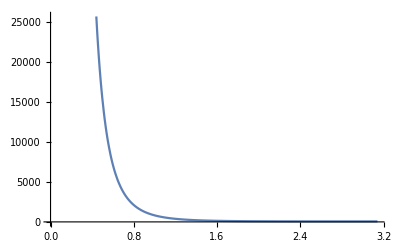

```mathematica
PR["• Plot of total cross-section as function of θ:",
NL,$=$tS/.$sT//Simplify,
Yield,$=$[[2]]/.e^4->512 π tu[Subscript[p, e[in]],0]^2
]
Plot[$,{θ,0,π}]
```

```mathematica
PR["• The θ functionality of the contributions from the different channels: ",NL,"t-channel",yield,$chant/.$sT//Simplify,
NL,"s-channel",yield,$chans/.$sT//Simplify,
NL,"u-channel",yield,$chanu/.$sT//Simplify,
NL,"show the divergent behavior comes from t-channel."
]
```

• The θ functionality of the contributions from the different channels: 
t-channel ⟶ e^4 (11+4 Cos[θ]+Cos[2 θ]) Csc[θ/2]^4
s-channel ⟶ 2 e^4 (3+Cos[2 θ])
u-channel ⟶ (8 e^4 (1+Cos[θ])^2)/(-1+Cos[θ])
show the divergent behavior comes from t-channel.